```mathematica
dataL = {{Degrees,Counts/30s,Counts/s, E},{180, 2569, 85.633, 9.25E},{170, 1509, 50.3, 7.09E},{160, 110, 3.667, 1.91},{157.5,49,1.63,127},{35,34,1.13,106.3},{190,1032,34.4, 586.5},{195,331,11.033,3.32},{200,58,1.933,139.03},{175,2400,80,894.4},{185,1998,66.6,816.1},{210,47,1.5667,125.2},{225,31,1.033,101.6}};
```

```mathematica
Grid[dataL, Alignment->Left,Spacings->{2,1}]
```

Degrees | (Counts s)/30 | Counts/s | ⅇ
180 | 2569 | 85.633 | 25.1441
170 | 1509 | 50.3 | 19.2726
160 | 110 | 3.667 | 1.91
157.5 | 49 | 1.63 | 127
35 | 34 | 1.13 | 106.3
190 | 1032 | 34.4 | 586.5
195 | 331 | 11.033 | 3.32
200 | 58 | 1.933 | 139.03
175 | 2400 | 80 | 894.4
185 | 1998 | 66.6 | 816.1
210 | 47 | 1.5667 | 125.2
225 | 31 | 1.033 | 101.6

```mathematica
(*dataC is a plot for degrees vs counts; {x,y}= {degrees,counts/s}*)
```

```mathematica
dataC = {{180, 85.633},{170,50.3},{160,3.667},{157.5,1.63},{35,1.13},{190,34.4},{195,11.033},{200,1.933},{175,80},{185,66.6},{210,1.5667},{225,1.033}};
Needs["ErrorBarPlots`"]
```

```mathematica
(*ErrorListPlot for dataC, the error bars are the square root of the count*)
```

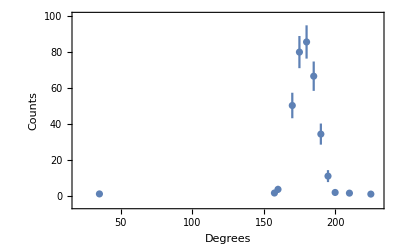

```mathematica
ErrorListPlot[{{{180,85.633},ErrorBar[Sqrt[85.633]]},{{170,50.3},ErrorBar[Sqrt[50.3]]},{{160,3.667},ErrorBar[Sqrt[3.667]]},{{157.5,1.63},ErrorBar[Sqrt[1.63]]},{{35,1.13},ErrorBar[Sqrt[1.13]]},{{190,34.4},ErrorBar[Sqrt[34.4]]},{{195,11.033},ErrorBar[Sqrt[11.033]]},{{200,1.933},ErrorBar[Sqrt[1.933]]},{{175,80},ErrorBar[Sqrt[80]]},{{185,66.6},ErrorBar[Sqrt[66.6]]},{{210,1.5667},ErrorBar[Sqrt[1.5667]]},{{225,1.033},ErrorBar[Sqrt[1.033]]}},Frame->True,FrameLabel->{"Degrees", "Counts"},PlotRange->{{20, 230},{-5,100}}]
```

```mathematica
(*dataD is a plot for degrees vs counts; {x,y}= {degrees,counts/30s}*)
```

```mathematica
dataD = {{180, 2569},{170,1509},{160,110},{157.5,49},{35,34},{190,1032},{195,331},{200,58},{175,2400},{185,1998},{210,47},{225,31}};
```

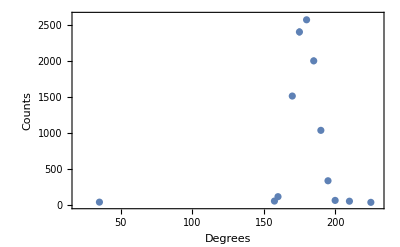

```mathematica
(*ErrorListPlot for dataD, the error bars are the square root of the count*)

ErrorListPlot[{{{180,2569},ErrorBar[Sqrt[569]]},{{170,1509},ErrorBar[Sqrt[1509]]},{{160,110},ErrorBar[Sqrt[110]]},{{157.5,49},ErrorBar[Sqrt[49]]},{{35,34},ErrorBar[Sqrt[34]]},{{190,1032},ErrorBar[Sqrt[1032]]},{{195,331},ErrorBar[Sqrt[331]]},{{200,58},ErrorBar[Sqrt[58]]},{{175,2400},ErrorBar[Sqrt[2400]]},{{185,1998},ErrorBar[Sqrt[1998]]},{{210,47},ErrorBar[Sqrt[47]]},{{225,31},ErrorBar[Sqrt[31]]}},Frame->True,FrameLabel->{"Degrees", "Counts"},PlotRange->{{20, 230},{-5,2620}}]
```

```mathematica
theta =N[ ArcTan[4/16],5]*(180/Pi)
```

14.036